# Mathematica Lab 3-Properties Z-Transform Representation

## Property-Convolution (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *07.12.2022*

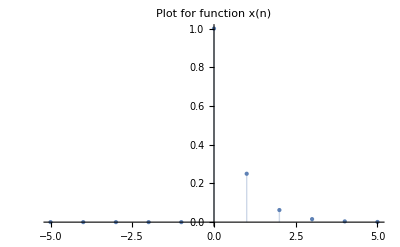

ConditionalExpression[(4 z)/(-1+4 z), Abs[z]>1/4]

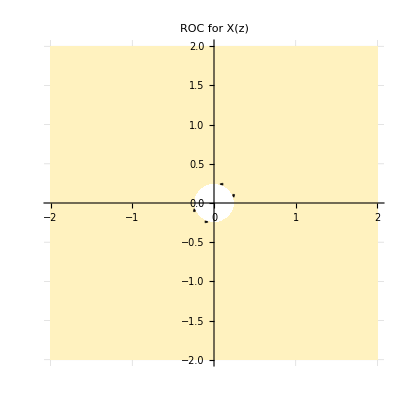

```mathematica
x[n_]:=(1/4)^n UnitStep[n];
(* This is Signal 1. *)
(* We are defining the signal itself here. *)
(* This signal is defiened in the TIME domain! *)

P1=ListPlot[Table[{n,x[n]},{n,-5,5}],Filling->Axis,PlotRange->All,PlotStyle->{PointSize[Large]},PlotLabel->"Plot for function x(n)"]
(* We Plot the signal function. See graph plot. *)


X[z_]=ZTransform[x[n],n,z,GenerateConditions->True]
(* This defines the Z-transform: *)

ROC=FullSimplify[(X[z]/Normal[X[z]])/.z->x+ⅈ y];
PX=ContourPlot[ROC/.a->2,{x,-2,2},{y,-2,2},AxesOrigin->{0,0},Frame->False,Axes->True,GridLines->Automatic,PlotLabel->"ROC for X(z)"]
(* This plots the Region of Convergence-ROC: *)
```

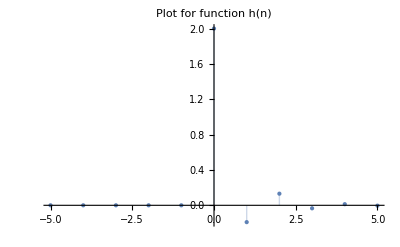

ConditionalExpression[(2 z (2+21 z))/((1+3 z) (-1+7 z)), Abs[z]>1/3]

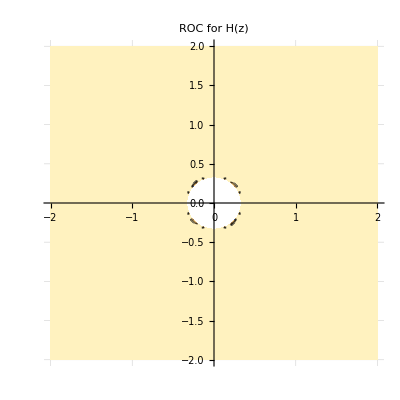

```mathematica
h[n_]:=(1/7)^n UnitStep[n]+(-1/3)^n UnitStep[n];
(* This is Signal 2. *)
(* We are defining the signal itself here. *)
(* This signal is defiened in the TIME domain! *)

P2=ListPlot[Table[{n,h[n]},{n,-5,5}],Filling->Axis,PlotRange->All,PlotStyle->{PointSize[Large]},PlotLabel->"Plot for function h(n)"]
(* We Plot the signal function. See graph plot. *)


H[z_]=ZTransform[h[n],n,z,GenerateConditions->True]
(* This defines the Z-transform: *)

ROC=FullSimplify[(H[z]/Normal[H[z]])/.z->x+ⅈ y];
PH=ContourPlot[ROC/.a->2,{x,-2,2},{y,-2,2},AxesOrigin->{0,0},Frame->False,Axes->True,GridLines->Automatic,PlotLabel->"ROC for H(z)"]
(* This plots the Region of Convergence-ROC: *)
```

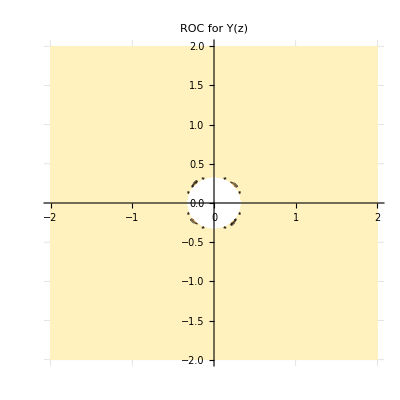

```mathematica
Y[Z_]:= X[z]*H[z];
(* Here we use Table TABLE 10.1-PROPERTIES OF THE z-TRANSFORM to get the Z-Transform Property of Convolution. *)
(* 10.5.7 *) (* We define this into a function Y(z) which is the function of X(z) multiplied with H(z). *)

ROC=FullSimplify[(Y[z]/Normal[Y[z]])/.z->x+ⅈ y];
PY=ContourPlot[ROC/.a->2,{x,-2,2},{y,-2,2},AxesOrigin->{0,0},Frame->False,Axes->True,GridLines->Automatic,PlotLabel->"ROC for Y(z)"]
(* This plots the Region of Convergence-ROC: *)
```

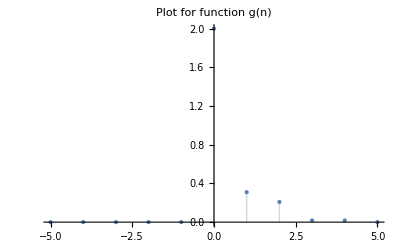

ConditionalExpression[(8 z^2 (2+21 z))/(1-8 z-5 z^2+84 z^3), Abs[z]>1/3]

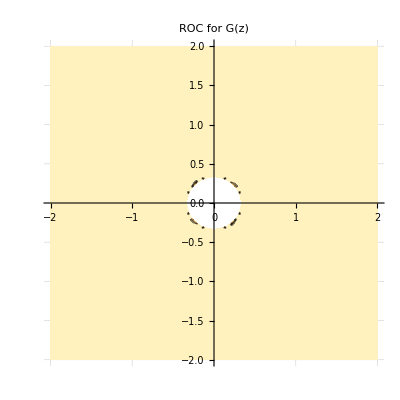

```mathematica
g[n_]=DiscreteConvolve[h[k],x[k],k,n];
(*  Here we are convolving the 2 signals in the TIME domain-normally using the given formula. *)

P3=ListPlot[Table[{n,g[n]},{n,-5,5}],Filling->Axis,PlotRange->All,PlotStyle->{PointSize[Large]},PlotLabel->"Plot for function g(n)"]
(* We Plot the signal function. See graph plot. *)

G[z_]=ZTransform[g[n],n,z,GenerateConditions->True]
(* This defines the Z-transform: *)

ROC=FullSimplify[(G[z]/Normal[G[z]])/.z->x+ⅈ y];
PG=ContourPlot[ROC/.a->2,{x,-2,2},{y,-2,2},AxesOrigin->{0,0},Frame->False,Axes->True,GridLines->Automatic,PlotLabel->"ROC for G(z)"]
(* This plots the Region of Convergence-ROC: *)
```

```mathematica
Simplify[Y[z]==G[z]]   (* We prove this is TRUE with both approaches, thus we prove the proeprty, for the ROC. *)
```

ConditionalExpression[True, Abs[z]>1/3]

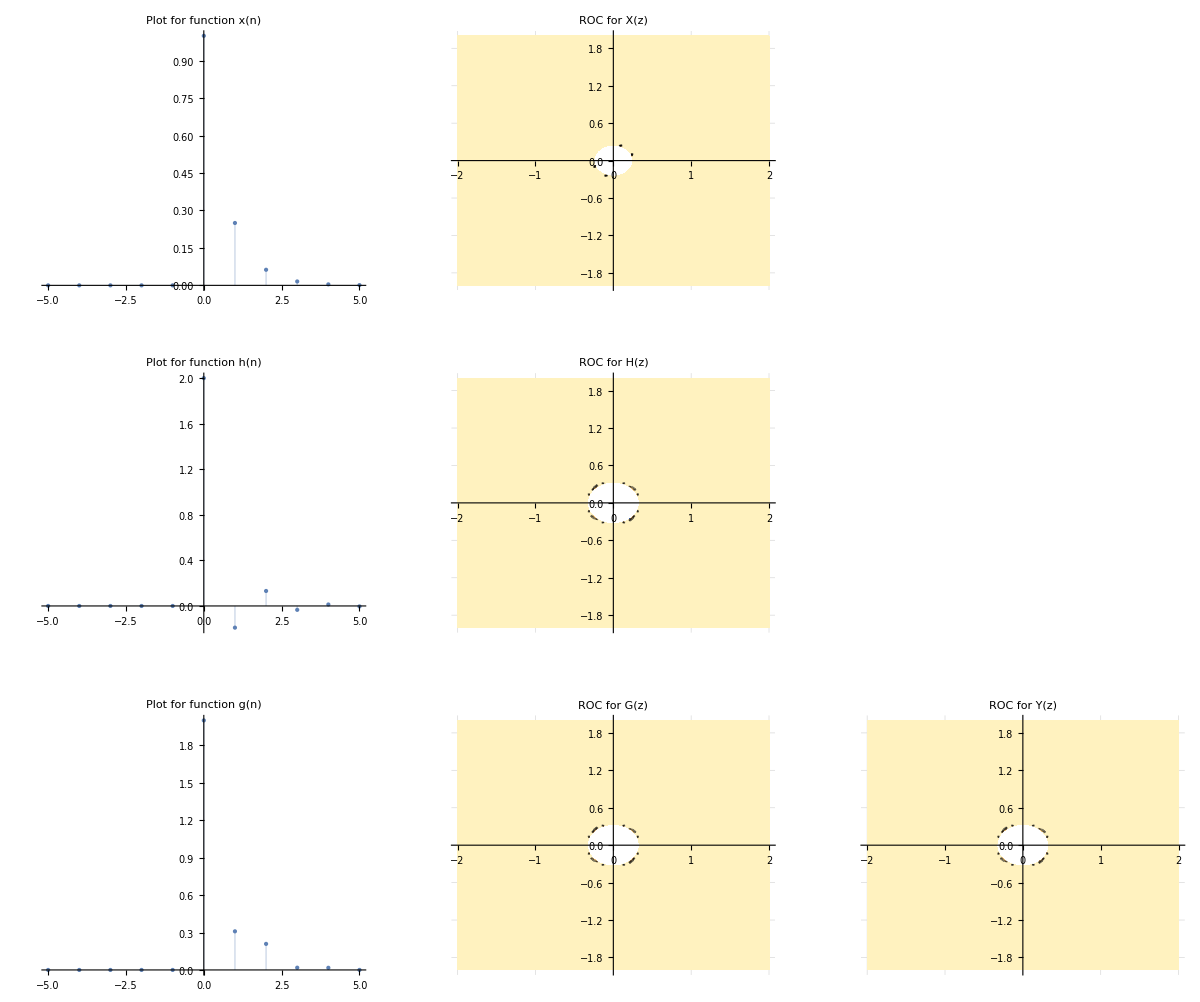

```mathematica
GraphicsGrid[{{P1,PX},{P2,PH},{P3,PG, PY}},Frame->True] (* Zoom out or scroll left to see all graphs. And we can compare ROC and functions Y[z] and H[z] visually and see they are the same, thus the property is TRUE. *)
```